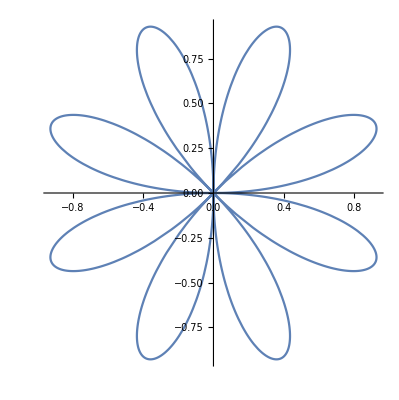

```mathematica
n = 3;
f[n_,θ_]:= Sin[n θ];
PolarPlot[f[4,θ],{θ,0,2π}]
ω = 1;
```

```mathematica
CoordinateTransform["Polar"-> "Cartesian",{Sin[3θ],θ}]
```

{Cos[θ] Sin[3 θ],Sin[θ] Sin[3 θ]}

```mathematica
animation = Table[Show[Graphics[{Red,Line[{{t,-1},{t,1}}]}],ContourPlot[{Sqrt[x^2+y^2]== Sin[3*(ArcTan[x,y]-10/2Sqrt[x^2+y^2] Cos[ArcTan[x,y]])]},{x,-1,t},{y,-1,1},PlotRange->{{-1,1},{-1,1}}]],{t,-.9,1,.1}]
```

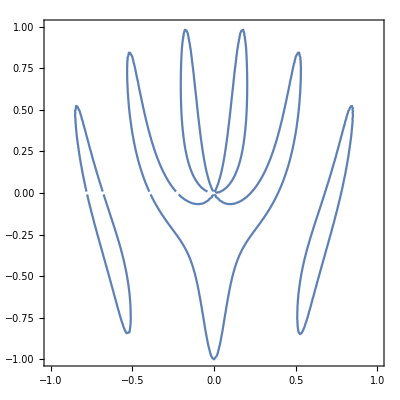

```mathematica
ContourPlot[{Sqrt[x^2+y^2]== Sin[3*(ArcTan[x,y]-10/2Sqrt[x^2+y^2] Cos[ArcTan[x,y]])]},{x,-1,1},{y,-1,1},PlotRange->{{-1,1},{-1,1}}]
```